```mathematica
chi21=Exp[-(x-3.1)^2/0.1]+Exp[-(x-2.7)^2/0.23]+Exp[-(x-3.2)^2/0.08]+Exp[-(x-2.89)^2/0.15];
chi22=Exp[-(x-2.1)^2/0.1]+Exp[-(x-1.7)^2/0.23]+Exp[-(x-2.2)^2/0.08]+Exp[-(x-1.89)^2/0.15];
```

```mathematica
chi21=Exp[-(x-3.1)^2/0.1-(x-2.7)^2/0.23-(x-3.2)^2/0.08-(x-2.89)^2/0.15];
chi22=Exp[-(x-2.1)^2/0.1-(x-1.7)^2/0.23-(x-2.2)^2/0.08-(x-1.89)^2/0.15];
```

```mathematica
NIntegrate[Exp[-(x-3.1)*(x-3.1)/0.1-(x-2.7)*(x-2.7)/0.23-(x-3.2)*(x-3.2)/0.08-(x-2.89)*(x-2.89)/0.15]+Exp[-(x-2.1)*(x-2.1)/0.1-(x-1.7)*(x-1.7)/0.23-(x-2.2)*(x-2.2)/0.08-(x-1.89)*(x-1.89)/0.15],{x,-Infinity,Infinity}]
```

0.223433

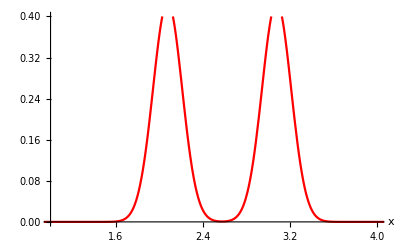

```mathematica
plotCHi2=Plot[chi21+chi22,{x,0,5},PlotRange->{{1,4},{0,0.4}},PlotStyle->{Red},AxesLabel->Automatic]
```

```mathematica
dist=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/1D/dist.txt","Table"];distRev=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/1D/distRev.txt","Table"];distConf=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/1D/distConf.txt","Table"];
```

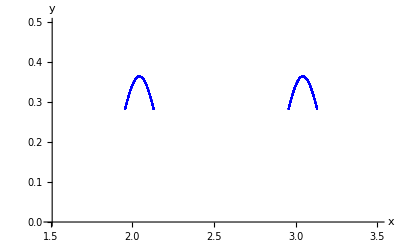

```mathematica
ListPlot[Table[{distConf[[i,2]],distConf[[i,1]]},{i,Length[distConf]}],AxesLabel->{"x","y"},PlotRange->{{1.5,3.5},{0,0.5}},PlotStyle->{Red,Blue}]
```

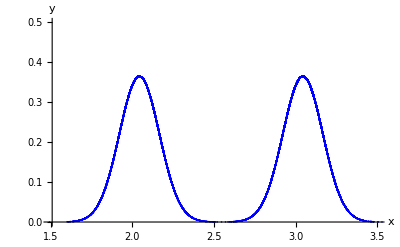

```mathematica
ListPlot[Table[{dist[[i,2]],dist[[i,1]]},{i,Length[dist]}],AxesLabel->{"x","y"},PlotRange->{{1.5,3.5},{0,0.5}},PlotStyle->{Red,Blue}]
```

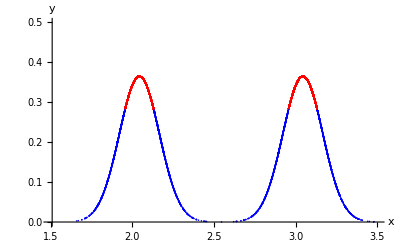

```mathematica
ListPlot[{Table[{distConf[[i,2]],distConf[[i,1]]},{i,Length[distConf]}],distMinusConf},AxesLabel->{"x","y"},PlotRange->{{1.5,3.5},{0,0.5}},PlotStyle->{Red,Blue}]
```

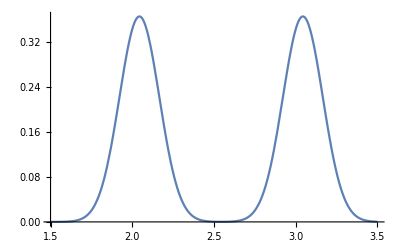

```mathematica
Plot[(Exp[-(x-3.1)*(x-3.1)/0.1-(x-2.7)*(x-2.7)/0.23-(x-3.2)*(x-3.2)/0.08-(x-2.89)*(x-2.89)/0.15]+Exp[-(x-2.1)*(x-2.1)/0.1-(x-1.7)*(x-1.7)/0.23-(x-2.2)*(x-2.2)/0.08-(x-1.89)*(x-1.89)/0.15]),{x,1.5,3.5},PlotRange->All]
```

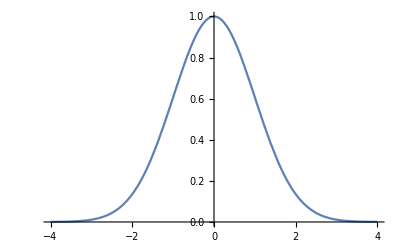

```mathematica
Plot[Exp[-x^2/2],{x,-4,4},PlotRange->All]
```

```mathematica
NIntegrate[Exp[-(x-1.2)^2/2/4],{x,-2.+1.2,2.+1.2}]/NIntegrate[Exp[-(x-1.2)^2/2/4],{x,-Infinity,Infinity}]
```

0.682689

```mathematica
NIntegrate[Exp[-(x-1.2)^2/2/0.2^2],{x,-Infinity,Infinity}]
```

0.501326

```mathematica
confPoints=Import["/home/sam/CloudStation/Project/04_Monte-Carlo/MCMCIntegrate/1D/confPoints.txt","Table"];
```

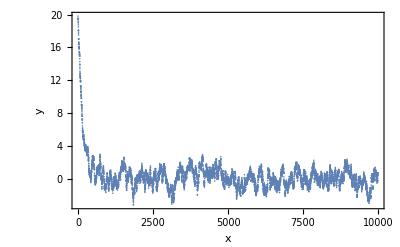

```mathematica
plotConf=ListPlot[confPoints,AxesLabel->{"x","y"},PlotRange->All,Frame->True]
```